# Computations for Complements

## Proofs of Propositions and Lemmas

## Centralization: proof of Lemma 1

### Demand functions

```mathematica
Demandsystem=Solve[p1==  α-q1 - γ q2 &&p2==  α-q2 - γ q1, {q1, q2}];
{{Q1, Q2}}= {q1,q2}/.Demandsystem
```

{{-(-p1+α+p2 γ-α γ)/(-1+γ^2),-(-p2+α+p1 γ-α γ)/(-1+γ^2)}}

### Profit functions

```mathematica
V= p1  Q1+ w2 Q2 ;
Subscript[Π, 2]=(p2-w2)Q2;
```

### First-Order Conditions

```mathematica
Print[" FOC_p1^C: ",D[V,p1]==0//FullSimplify ]
Print[" FOC_p2^C: ",D[Subscript[Π, 2],p2]==0//FullSimplify]
```

FOC_p1^C: (2 p1+α (-1+γ)-(p2+w2) γ)/(-1+γ^2)==0

FOC_p2^C: (-2 p2+w2+α+p1 γ-α γ)/(-1+γ^2)==0

### Second-Order Conditions

```mathematica
Print[" SOC_p1^C: ",D[D[V,p1],p1]//FullSimplify ]
Print[" SOC_p2^C: ",D[D[Subscript[Π, 2],p2],p2]//FullSimplify]
```

SOC_p1^C: 2/(-1+γ^2)

SOC_p2^C: 2/(-1+γ^2)

### Sub-game optimal prices

```mathematica
FOCsubC=Solve[D[V,p1]==0&&D[Subscript[Π, 2],p2]==0, {p1,p2}] //FullSimplify ;
{{p1sub, p2sub}}={p1,p2} /. FOCsubC
```

{{(-3 w2 γ+α (-2+γ+γ^2))/(-4+γ^2),(-w2 (2+γ^2)+α (-2+γ+γ^2))/(-4+γ^2)}}

Rewrite solutions:

```mathematica
(-3 w2 γ+α (-2+γ+γ^2))/(-4+γ^2)== (α (1-γ)(2+γ)+2 C1+  w2 γ)/(4-γ^2)/.C1->  w2 γ//FullSimplify (* p1(w2) *)
(-w2 (2+γ^2)+α (-2+γ+γ^2))/(-4+γ^2)== (α (1-γ)(2+γ)+  2 w2 +γ C1)/(4-γ^2)/.C1->  w2 γ//FullSimplify (* p2(w2) *)
```

True

True

```mathematica
Print[" p_1^C(w_2) = ",(α (1-γ)(2+γ)+2 C1+  w2 γ)/(4-γ^2) ]
Print[" p_2^C(w_2) = ",(α (1-γ)(2+γ)+  2 w2 +γ C1)/(4-γ^2)]
```

p_1^C(w_2) = (2 C1+w2 γ+α (1-γ) (2+γ))/(4-γ^2)

p_2^C(w_2) = (2 w2+C1 γ+α (1-γ) (2+γ))/(4-γ^2)

### Monopolist’s expected profit

```mathematica
ExpV=p1 Q1+ w2 Q2 /.p1-> p1sub /. p2->  p2sub //FullSimplify;
```

### First-Order (necessary) Condition

```mathematica
Print[" FOC_w2^C: ",D[ExpV,w2]==0//FullSimplify ]
```

FOC_w2^C: (-2 w2 (8+γ^2)+α (8+γ^3))/(-4+γ^2)==0

### Second-Order Condition

```mathematica
Print[" SOC_w2^C: ",D[D[ExpV,w2],w2]//FullSimplify ]
D[D[ExpV,w2],w2]< 0 &&-1<γ<= 0//FullSimplify  (* product complements hypothesis *)
```

SOC_w2^C: -(2 (8+γ^2))/((-4+γ^2)^2)

-1<γ≤0

### Optimal input price

```mathematica
SolP = Solve[ D[ExpV,w2]==0 , w2] //FullSimplify ;
{{w2starC}}={w2}/. SolP
```

{{(α (8+γ^3))/(2 (8+γ^2))}}

Rewrite solution :

```mathematica
(α (8+γ^3))/(2 (8+γ^2))==α/2-(α (1-γ)γ^2)/(2 (8+γ^2))//FullSimplify  (* w2 *)
```

True

```mathematica
Print[" w_2^C = ",α/2-(α (1-γ)γ^2)/(2 (8+γ^2))]
```

w_2^C = α/2-(α (1-γ) γ^2)/(2 (8+γ^2))

### Equilibrium values

```mathematica
Print["p_1^C = ",Factor[p1starC = p1sub /.w2-> w2starC//Simplify]]
Print["p_2^C = ",Factor[p2starC=p2sub /.w2-> w2starC//Simplify]]
D1starC=Q1 /.p2-> p2sub /.p1-> p1sub/.w2-> w2starC//Simplify;
D2starC= Q2 /.p2-> p2sub /.p1-> p1sub/.w2-> w2starC//Simplify;
Print["V^C = ",Factor[VstarC=p1 Q1 + w2 Q2 /.p2-> p2sub /.p1-> p1sub/.w2-> w2starC//Simplify]]
Print["Π_2^C = ",Factor[pi2starC=(p2-w2)Q2/.p2-> p2sub /.p1-> p1sub/.w2-> w2starC//Simplify]]
Print["CS^C = ",CSstarC=(Q1^2+2γ Q1 Q2 + Q2^2)/2/.p2-> p2sub /.p1-> p1sub/.w2-> w2starC//Simplify]
```

p_1^C = -(α (-4+γ) (2+γ))/(2 (8+γ^2))

p_2^C = -(α (-12+4 γ-2 γ^2+γ^3))/(2 (8+γ^2))

V^C = (α^2 (2+γ) (6-γ+γ^2))/(4 (1+γ) (8+γ^2))

Π_2^C = -(α^2 (-1+γ) (2+γ^2)^2)/((1+γ) (8+γ^2)^2)

CS^C = (α^2 (80+16 γ+36 γ^2+24 γ^3+γ^4+5 γ^5))/(8 (1+γ) (8+γ^2)^2)

Rewrite solutions:

```mathematica
FullSimplify[-(α (-4+γ) (2+γ))/(2 (8+γ^2))==(α (4-γ) (2+γ))/(2 (8+γ^2))] (* p1 *)
FullSimplify[-(α (-12+4 γ-2 γ^2+γ^3))/(2 (8+γ^2))==(α (2(6+γ^2)-γ(4+γ^2)))/(2 (8+γ^2))] (* p2 *)
```

True

True

```mathematica
Print["p_1^C = ",(α (4-γ) (2+γ))/(2 (8+γ^2))]
Print["p_2^C = ",(α (2(6+γ^2)-γ(4+γ^2)))/(2 (8+γ^2))]
Print["V^C = ",VstarC]
Print["Π_2^C = ",pi2starC]
Print["CS^C = ",CSstarC]
```

p_1^C = (α (4-γ) (2+γ))/(2 (8+γ^2))

p_2^C = (α (-γ (4+γ^2)+2 (6+γ^2)))/(2 (8+γ^2))

V^C = (α^2 (12+4 γ+γ^2+γ^3))/(4 (1+γ) (8+γ^2))

Π_2^C = -(α^2 (-1+γ) (2+γ^2)^2)/((1+γ) (8+γ^2)^2)

CS^C = (α^2 (80+16 γ+36 γ^2+24 γ^3+γ^4+5 γ^5))/(8 (1+γ) (8+γ^2)^2)

## Decentralization with *observable* contracts: proof of Lemma 2 and 3.

### New Profit functions

```mathematica
Subscript[Π, 1]= (p1 -w1) Q1;
Subscript[Π, 2]=(p2-w2)Q2 ;
```

### First-Order Conditions

```mathematica
Print[" FOC_p1^C: ", D[Subscript[Π, 1],p1]==0//FullSimplify ]
Print[" FOC_p2^C: ",D[Subscript[Π, 2],p2]==0//FullSimplify]
```

FOC_p1^C: (-2 p1+w1+α+p2 γ-α γ)/(-1+γ^2)==0

FOC_p2^C: (-2 p2+w2+α+p1 γ-α γ)/(-1+γ^2)==0

### Second-Order Conditions

```mathematica
Print[" SOC_p1^C: ", D[D[Subscript[Π, 1],p1],p1]//FullSimplify ]
Print[" SOC_p2^C: ",D[D[Subscript[Π, 2],p2],p2]//FullSimplify]
```

SOC_p1^C: 2/(-1+γ^2)

SOC_p2^C: 2/(-1+γ^2)

### Sub-game optimal prices

```mathematica
FOCsubD=Solve[D[Subscript[Π, 1],p1]==0&&D[Subscript[Π, 2],p2]==0, {p1,p2}] //FullSimplify;
{{p1subD, p2subD}}={p1,p2} /. FOCsubD
```

{{(-2 w1-w2 γ+α (-2+γ+γ^2))/(-4+γ^2),(-2 w2-w1 γ+α (-2+γ+γ^2))/(-4+γ^2)}}

```mathematica
Print["p_1^D(w1, w2) = ", p1subD ]
Print["p_2^D(w2,w1) = ", p2subD ]
```

p_1^D(w1, w2) = (-2 w1-w2 γ+α (-2+γ+γ^2))/(-4+γ^2)

p_2^D(w2,w1) = (-2 w2-w1 γ+α (-2+γ+γ^2))/(-4+γ^2)

### Monopolist’s expected profit

```mathematica
ExpVD=p1 Q1+ w2 Q2  /.p1-> p1subD /. p2->  p2subD//FullSimplify;
```

### First-Order Conditions

```mathematica
Print[" FOC_w1^D: ", D[ExpVD,w1]==0//FullSimplify ]
Print[" FOC_w2^D: ",D[ExpVD,w2]==0//FullSimplify]
```

FOC_w1^D: (-4 w1 (-2+γ^2)+γ (-4 w2+α γ (-2+γ+γ^2)))/(4-5 γ^2+γ^4)==0

FOC_w2^D: (4 w1 γ-2 w2 (8-7 γ^2+γ^4)+α (8+γ^2 (-8+(-1+γ) γ)))/(4-5 γ^2+γ^4)==0

### Second-Order Condition (Hessian matrix)

```mathematica
Print[" SOC_(w1, w2)^D: "," minors d°1 (<0): ",  D[D[ExpVD,w1],w1] &&  D[D[ExpVD,w2],w2]," minor d°2 (>0): ",   D[D[ExpVD,w1],w1] *   D[D[ExpVD,w2],w2]-   D[D[ExpVD,w1],w2]  D[D[ExpVD,w2],w1] //FullSimplify ]
```

SOC_(w1, w2)^D:  minors d°1 (<0): -(4 (-2+γ^2))/((-4+γ^2)^2 (-1+γ^2))&&(2 (8-7 γ^2+γ^4))/((-4+γ^2)^2 (-1+γ^2)) minor d°2 (>0): -8/((-4+γ^2)^2 (-1+γ^2))

### Optimal input price

```mathematica
SolD = Solve[D[ExpVD,w1]==0 && D[ExpVD,w2]==0 , {w1,w2}] //FullSimplify ;
{{w1starD, w2starD}}={w1,w2}/. SolD
```

{{1/4 α γ (1+γ),α/2}}

Rewrite solutions:

```mathematica
FullSimplify[1/4 α γ (1+γ)==γ(α/2-(α(1-γ))/4)]
```

True

```mathematica
Print[" w_1^D: ",γ(α/2-(α(1-γ))/4)]
Print[" w_2^D: ",w2starD]
```

w_1^D: (α/2-1/4 α (1-γ)) γ

w_2^D: α/2

### Equilibrium values

```mathematica
Print["p_1^P = ",Factor[p1starD = p1subD /.w2-> w2starD /.w1-> w1starD//Simplify]]
Print["p_2^P = ",Factor[p2starD=p2subD /.w2-> w2starD /.w1-> w1starD//Simplify]]
D1starD=Q1/.p1-> p1subD/.p2-> p2subD/.w2-> w2starD /.w1-> w1starD//Simplify;
D2starD= Q2 /.p1-> p1subD/.p2-> p2subD/.w2-> w2starD /.w1-> w1starD //Simplify;
Print["V^P = ",Factor[VstarD=p1 Q1+ w2 Q2/.p1-> p1subD/.p2-> p2subD/.w2-> w2starD /.w1-> w1starD//Simplify]]
Print["Π_2^P = ",Factor[pi2starD=(p2-w2)Q2/.p1-> p1subD/.p2-> p2subD/.w2-> w2starD /.w1-> w1starD//Simplify]]
Print["CS^P = ",CSstarD= (Q1^2+2 γ Q1 Q2 + Q2^2)/2/.p1-> p1subD/.p2-> p2subD/.w2-> w2starD /.w1-> w1starD//Simplify]
```

p_1^P = α/2

p_2^P = -1/4 α (-3+γ)

V^P = (α^2 (3+γ))/(8 (1+γ))

Π_2^P = -(α^2 (-1+γ))/(16 (1+γ))

CS^P = (α^2 (5+3 γ))/(32 (1+γ))

## Proof of Proposition 6

```mathematica
(* |Subscript[w, 1]^D| <= |Subscript[C, 1](Subscript[w, 2])| *)
w1starD - γ w2starC //FullSimplify;
Reduce[Abs[w1starD ]<=Abs[ γ w2starC ] &&  α>0 &&-1<γ<= 0]//FullSimplify (* product complements hypothesis *)
```

α>0&&-1<γ≤0

```mathematica
(* Subscript[w, 2]^D >= Subscript[w, 2]^C *)
w2starD - w2starC //FullSimplify;
Reduce[w2starD >= w2starC  &&  α>0 && -1<γ<= 0]//FullSimplify (* product complements hypothesis *)
```

α>0&&-1<γ≤0

## Proof of Proposition 7

```mathematica
(* Subscript[p, 1]^D >= Subscript[p, 1]^C *)
p1starD - p1starC //FullSimplify;
Reduce[p1starD >= p1starC &&  α>0 && -1<  γ <=  0]//FullSimplify
```

α>0&&-1<γ≤0

```mathematica
(* Subscript[p, 2]^D <= Subscript[p, 2]^C *)
p2starD - p2starC //FullSimplify;
Reduce[p2starD <= p2starC  &&  α>0 && -1 <  γ<= 0]//FullSimplify
```

α>0&&-1<γ≤0

## Proof of Proposition 8

### Recall products are substitutes in the file: 1> γ > 0

```mathematica
(* V^D >= V^C *)
Reduce[VstarD > VstarC &&  α>0 &&-1<γ<= 0]//FullSimplify (* product complements hypothesis *)
(* Subscript[π, 2]^D <= Subscript[π, 2]^C *)
Reduce[pi2starD < pi2starC &&  α>0 &&-1<γ<= 0]//FullSimplify (* product complements hypothesis *)
(* Subscript[CS, 2]^D <= Subscript[CS, 2]^C *)
Reduce[CSstarD < CSstarC &&  α>0 &&-1<γ<= 0]//FullSimplify (* product complements hypothesis *)
```

α>0&&-1<γ<0

α>0&&-1<γ<0

α>0&&-1<γ<0

## Proof Figure 2: comparative statics for complements

```mathematica
DP = p1starD D1starD-p1starC D1starC/.α-> 1//FullSimplify;
UP= w2starD D2starD - w2starC D2starC/.α-> 1//FullSimplify;
DeltaPi=VstarD-VstarC/.α-> 1//FullSimplify;
```

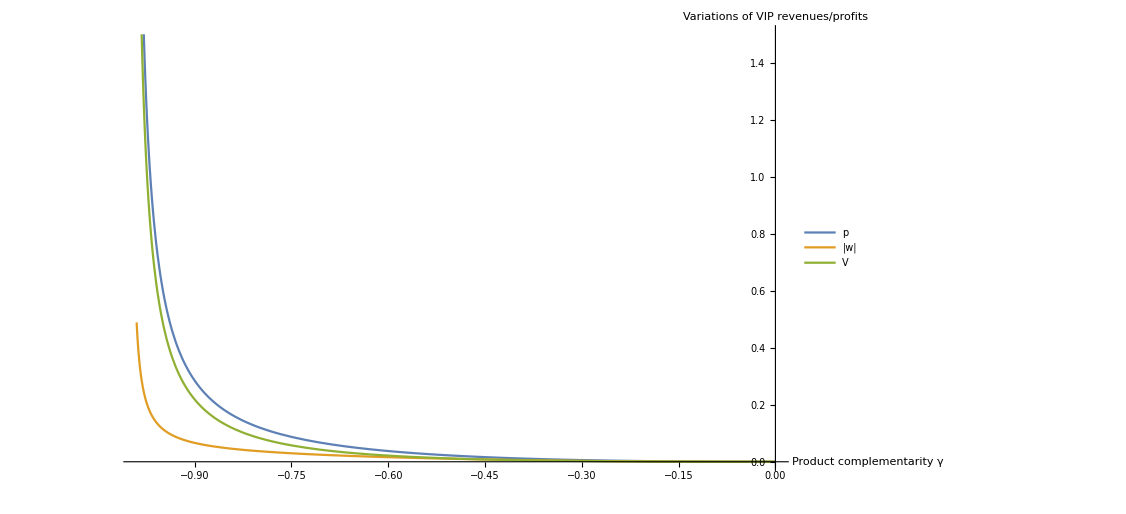

```mathematica
DPgraph=Plot[{DP, -UP, DeltaPi}, {γ,-0.99,0}, 
PlotRange-> {{-0.99, 0}, {0, 1.5}}, 
PlotLegends->Placed[LineLegend[{"p", "|w|", "V"}, LegendFunction->"Frame"], {0.65,0.45}], AxesLabel->{Style["Product complementarity γ",Bold,16], Style["Variations of VIP revenues/profits",Bold,16]}] (* product complements hypothesis *)
```

## Private transfer to the downstream unit

### Decentralized Profit Functions

```mathematica
Subscript[Π, 1]= (p1 -w1) Q1;
Subscript[Π, 2]=(p2-w2)Q2 ;
```

### First Order Conditions and Reaction functions

```mathematica
Print[" p_2^h(w_2, (p̃)_1)= ",R2M=Extract[p2/.Solve[D[Subscript[Π, 2],p2]==0,p2],1]/. p1-> p1b//FullSimplify]
Print[" R_1^h(w_1, p_2)= ",Extract[p1/.Solve[D[Subscript[Π, 1],p1]==0,p1],1]//FullSimplify]
Print[" p_1^h(w_1, w_2, (p̃)_1)= ",R1M=Extract[p1/.Solve[D[Subscript[Π, 1],p1]==0,p1],1]/. p2-> R2M//FullSimplify]
```

p_2^h(w_2, (p̃)_1)= 1/2 (w2+α+p1b γ-α γ)

R_1^h(w_1, p_2)= 1/2 (w1+α+p2 γ-α γ)

p_1^h(w_1, w_2, (p̃)_1)= 1/4 (2 w1+γ (w2+p1b γ)-α (-2+γ+γ^2))

### Monopolist’s expected profit

```mathematica
ExpVM=p1 Q1+ w2 Q2/.p1-> R1M/. p2->  R2M //FullSimplify;
```

### First-Order Conditions

```mathematica
Print[" FOC_w_1^h: ", D[ExpVM,w1]==0//Simplify ]
Print[" FOC_w_2^h: ", D[ExpVM,w2] ==0//Simplify ]
```

FOC_w_1^h: (w1-w2 γ)/(-1+γ^2)==0

FOC_w_2^h: (w2 (-8+5 γ^2)+γ (-4 p1b+4 w1+3 p1b γ^2)+α (4+2 γ-3 γ^2-3 γ^3))/(-1+γ^2)==0

### Second-Order Conditions

```mathematica
Print[" SOC minor_w_2 d°1 : ",D[D[ExpVM, w2],w2] //FullSimplify,  " < 0, for all ", 
Reduce[D[D[ExpVM, w2],w2] <0  && α ≥ 0 &&-1<γ<= 0]//FullSimplify]
Print[" SOC minor_w_1 d°1 (<0): ",D[D[ExpVM, w1],w1] //FullSimplify , " < 0, for all ",
Reduce[D[D[ExpVM, w1],w1] <0  && α ≥ 0 && -1<γ<= 0]//FullSimplify]
Print[" SOC minor d°2 (>0) : ",D[D[ExpVM, w1],w1]D[D[ExpVM, w2],w2] - D[D[ExpVM, w2],w1] D[D[ExpVM, w1],w2] //FullSimplify , " is positive if : ", Reduce[D[D[ExpVM, w1],w1]D[D[ExpVM, w2],w2] - D[D[ExpVM, w2],w1] D[D[ExpVM, w1],w2] >0  && α ≥ 0 && -1<γ<= 0]//FullSimplify]
```

SOC minor_w_2 d°1 : (8-5 γ^2)/(8 (-1+γ^2)) < 0, for all α≥0&&-1<γ≤0

SOC minor_w_1 d°1 (<0): 1/(2 (-1+γ^2)) < 0, for all α≥0&&-1<γ≤0

SOC minor d°2 (>0) : (8-9 γ^2)/(16 (-1+γ^2)^2) is positive if : α≥0&&-(2 √2)/3<γ≤0

### Optimal input prices

```mathematica
SolM = Solve[D[ExpVM,w2]==0  && D[ExpVM,w1]==0 &&p1b== R1M, {w1,w2, p1b}] //FullSimplify  ;
{{w1starM, w2starM, p1starM}}={w1,w2, p1b}/.SolM
```

{{(α γ (2+γ)^2)/(8 (1+γ)),(α (2+γ)^2)/(8 (1+γ)),(α (4+5 γ))/(8 (1+γ))}}

### Equilibrium values

```mathematica
Print["p_2^h = ",Factor[p2starM=R2M /.w2-> w2starM /.w1-> w1starM/.p1b-> p1starM//Simplify]]
D1starM=Q1 /.p1-> p1starM/.p2-> p2starM/.w2-> w2starM /.w1-> w1starM//Simplify;
D2starM= Q2/.p1-> p1starM/.p2-> p2starM/.w2-> w2starM /.w1-> w1starM//Simplify;
Print["V^h = ",Factor[VstarM=p1 Q1+ w2 Q2  /.p1-> p1starM/.p2-> p2starM/.w2-> w2starM /.w1-> w1starM//Simplify]]
Print["Π_2^h = ",Factor[pi2starM=(p2-w2)Q2/.p1-> p1starM/.p2-> p2starM/.w2-> w2starM /.w1-> w1starM//Simplify]]
Print["CS^h = ",CSstarM= (Q1^2+2γ Q1 Q2 + Q2^2)/2/.p1-> p1starM/.p2-> p2starM//Simplify]
```

p_2^h = -(α (-6-4 γ+γ^2))/(8 (1+γ))

V^h = (α^2 (24+32 γ+7 γ^2))/(64 (1+γ)^2)

Π_2^h = -(α^2 (-1+γ))/(16 (1+γ))

CS^h = (α^2 (20+24 γ+5 γ^2))/(128 (1+γ)^2)

### Comparison with centralization

```mathematica
(* V^h <= V^C *)
Reduce[VstarM <VstarC  && α ≥ 0 && -(2 √2)/3<γ≤0]//FullSimplify
```

-(2 √2)/3<γ<0&&α>0